```mathematica
e = 1.602176487 10^-19;
ℏ=6.626 10^-34(*J s*);
c=299792458 ;
me=9.10938215 10^-31 ;
mp=1.672621637 10^-27 ;
gp=5.585694713;
ge=-2.00231904622;
μ0=4 π 10^-7;
ϵ0= 1/(μ0 c^2)//N;
α=e^2/((4π ϵ0)ℏ c);
a=ℏ/(me c α);
μe=-ge (e ℏ)/(2me)
μp=gp (e ℏ)/(2 mp) 
γe=μe/ℏ (* in rad/s = 1/2π Hz *)
γp=μp/ℏ(* in rad/s *)
r0=10^-10; (*m *)
A0=μ0/(4π)γe γp ℏ/r0^3
```

1.16675×10^-22

1.7726×10^-25

1.76086×10^11

2.67522×10^8

3.1213×10^9

```mathematica
{64.2/1000 γp/(2π 10^6),64.2/1000 γe/(2π 10^6)}
```

{17.1749,11304.7}

```mathematica
Jz=1/2{{1,0},{0,-1}};
Jx=1/2{{0,1},{1,0}};
Jy=1/2{{0,-ⅈ},{ⅈ,0}};
II={{1,0},{0,1}};
RGB[θ_]:=If[0≤ θ<120,RGBColor[Cos[θ/120 π/2],Sin[θ/120 π/2],0],
If[120≤ θ<240,RGBColor[0,Cos[(θ-120)/120 π/2],Sin[(θ-120)/120 π/2]],
If[240≤ θ<360,RGBColor[Sin[(θ-240)/120 π/2],0,Cos[(θ-240)/120 π/2]],0],0],0]
```

```mathematica
(* direct Product space *)
```

```mathematica
I4=IdentityMatrix[4];
Sz=KroneckerProduct[Jz,II];
Sx=KroneckerProduct[Jx,II];
Sy=KroneckerProduct[Jy,II];
Sp=KroneckerProduct[Jx+ⅈ Jy,II];
Sm=KroneckerProduct[Jx-ⅈ Jy,II];
Iz=KroneckerProduct[II,Jz];
Ix=KroneckerProduct[II,Jx];
Iy=KroneckerProduct[II,Jy];
SzIz=KroneckerProduct[Jz,Jz];
SzIy=KroneckerProduct[Jz,Jy];
SxIx=KroneckerProduct[Jx,Jx];
SxIy=KroneckerProduct[Jx,Jy];
SyIy=KroneckerProduct[Jy,Jy];
SzIx=KroneckerProduct[Jz,Jx];
SzIy=KroneckerProduct[Jz,Jy];
SxIz=KroneckerProduct[Jx,Jz];
SpIm=KroneckerProduct[Jx+ⅈ Jy,Jx-ⅈ Jy];
SmIp=KroneckerProduct[Jx-ⅈ Jy,Jx+ⅈ Jy];
SpIp=KroneckerProduct[Jx+ⅈ Jy,Jx+ⅈ Jy];
SmIm=KroneckerProduct[Jx-ⅈ Jy,Jx-ⅈ Jy];
SzIp=KroneckerProduct[Jz,Jx+ⅈ Jy];
SzIm=KroneckerProduct[Jz,Jx-ⅈ Jy];
```

```mathematica
S1Iy=KroneckerProduct[1/2 II+Jz,Jy];
S1Iz=KroneckerProduct[1/2 II+Jz,Jz];
S1Ix=KroneckerProduct[1/2 II+Jz,Jx];
S2Iz=KroneckerProduct[1/2 II-Jz,Jz];
S2Iy=KroneckerProduct[1/2 II-Jz,Jy];
S2Ix=KroneckerProduct[1/2 II-Jz,Jx];
```

```mathematica
{DD=1384.5,EE=-42.5};
Manipulate[
{γp/(2π 10^6) H/1000,
-(DD-3EE)/6+1/2 √((DD+EE)^2+4(γe/(10^6 2π))^2( H/1000)^2),
DD/3-EE,
-(DD-3EE)/6-1/2 √((DD+EE)^2+4(γe/(10^6 2π))^2(H/1000)^2)
}
,
{{H,64.5,"H [mT]"},0.064}]
```

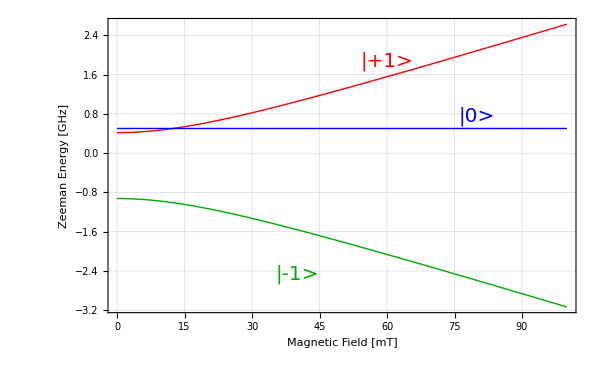

```mathematica
Plot[
Evaluate[1/1000{
-(DD-3EE)/6+1/2 √((DD+EE)^2+4(γe/(10^6 2π))^2( H/1000)^2),
DD/3-EE,
-(DD-3EE)/6-1/2 √((DD+EE)^2+4(γe/(10^6 2π))^2(H/1000)^2)
}],{H,0,100},PlotStyle->{Red,Blue,Darker[Green]},
Epilog->{Text[Style["|+1>",Red,20],{60,(-(DD-3EE)/6+1/2 √((DD+EE)^2+4(γe/(10^6 2π))^2( 60/1000)^2))1.2/1000}],
Text[Style["|0>",Blue,20],{80,(DD/3-EE)1.5/1000}],
Text[Style["|-1>",Darker[Green],20],{40,(-(DD-3EE)/6-1/2 √((DD+EE)^2+4(γe/(10^6 2π))^2( 60/1000)^2))1.2/1000}]},
GridLines->Automatic,GridLinesStyle->Directive[Gray,Dotted],FrameStyle->Directive[Black,20],
Frame->True,FrameLabel->{Style["Magnetic Field [mT]",20],Style["Zeeman Energy [GHz]",20]},ImageSize->600]
```

```mathematica
Solve[-(DD-3EE)/6-1/2 √((DD+EE)^2+4(γe/(10^6 2π))^2(H/1000)^2)==-8407.5,H]
```

{{H→-290.022},{H→290.022}}

```mathematica
HR[ΩS_,ΩI_,Ωu_,ω_,Azz_,Azx_]:=(ΩS+ω) Sz+Ωu Sx+ΩI Iz+Azz SzIz+Azx SzIx
HR[ΩS,ΩI,Ωu,ω,Azz,Azx]//MatrixForm
```

(Azz/4+ΩI/2+(ω+ΩS)/2 | Azx/4 | Ωu/2 | 0
Azx/4 | -Azz/4-ΩI/2+(ω+ΩS)/2 | 0 | Ωu/2
Ωu/2 | 0 | -Azz/4+ΩI/2+1/2 (-ω-ΩS) | -Azx/4
0 | Ωu/2 | -Azx/4 | Azz/4-ΩI/2+1/2 (-ω-ΩS))

```mathematica
Pe[t_,ΩS_,ΩI_,Ωu_,ω_,Azz_,Azx_,P_,j_]:=2Tr[Sz.MatrixExp[-ⅈ HR[ΩS,ΩI,Ωu,ω,Azz,Azx] t].(IdentityMatrix[4] 1/4 +P/2 Sz+j/2 Iz+P j SzIz).MatrixExp[ⅈ HR[ΩS,ΩI,Ωu,ω,Azz,Azx] t]]//FullSimplify
PI[t_,ΩS_,ΩI_,Ωu_,ω_,Azz_,Azx_,P_,j_]:=2Tr[Iz.MatrixExp[-ⅈ HR[ΩS,ΩI,Ωu,ω,Azz,Azx] t].(IdentityMatrix[4] 1/4 +P/2 Sz+j/2 Iz+P j SzIz).MatrixExp[ⅈ HR[ΩS,ΩI,Ωu,ω,Azz,Azx] t]]//FullSimplify
```

```mathematica
PeA[t_,A_,θ_,B_,P_,j_]:=2Tr[Cos[θ]Sz.MatrixExp[-ⅈ t A Cos[θ] SzIz+ⅈ t B/4 Sin[θ](SpIm+SmIp)].(IdentityMatrix[4] 1/4 +P/2 Cos[θ]Sz+j/2 Iz+P j Cos[θ]SzIz).MatrixExp[ⅈ A t Cos[θ] SzIz-ⅈ t B/4 Sin[θ](SpIm+SmIp)]]//FullSimplify
PIA[t_,A_,θ_,B_,P_,j_]:=2Tr[Iz.MatrixExp[-ⅈ t A Cos[θ] SzIz+ⅈ t B/4 Sin[θ](SpIm+SmIp)].(IdentityMatrix[4] 1/4 +P/2 Cos[θ]Sz+j/2 Iz+P j Cos[θ]SzIz).MatrixExp[ⅈ A t Cos[θ] SzIz-ⅈ t B/4 Sin[θ](SpIm+SmIp)]]//FullSimplify
```

```mathematica
PeA[t,A,θ,B,P,j]//Expand
PIA[t,A,θ,B,P,j]
```

P Cos[θ]^2 Cos[1/4 B t Sin[θ]]^2+j Cos[θ] Sin[1/4 B t Sin[θ]]^2

j Cos[1/4 B t Sin[θ]]^2+P Cos[θ] Sin[1/4 B t Sin[θ]]^2

```mathematica
Solve[√((-8407.5+8408)^2+Ωu^2)-12.77==0,Ωu][[2]]
```

{Ωu→12.7602}

```mathematica
Manipulate[
GraphicsGrid[{{
Plot[
{Pe[t,ΩS,ΩI,Ωu,ω,A0(1-3 Cos[θ]^2),-3/2 A0 Sin[2θ],P,j],
PI[t,ΩS,ΩI,Ωu,ω,A0(1-3 Cos[θ]^2),-3/2 A0 Sin[2θ],P,j],
(* for Hartmann-hAhn condition fullfilled *)
P ((ΩS+ω)/(√((ΩS+ω)^2+Ωu^2)))^2 Cos[1/4 -3/2 A0 Sin[2θ] t Ωu/(√((ΩS+ω)^2+Ωu^2))]^2+j (ΩS+ω)/(√((ΩS+ω)^2+Ωu^2)) Sin[1/4 -3/2 A0 Sin[2θ] t Ωu/(√((ΩS+ω)^2+Ωu^2))]^2,
j Cos[1/4 -3/2 A0 Sin[2θ] t Ωu/(√((ΩS+ω)^2+Ωu^2))]^2+P (ΩS+ω)/(√((ΩS+ω)^2+Ωu^2)) Sin[1/4 -3/2 A0 Sin[2θ] t Ωu/(√((ΩS+ω)^2+Ωu^2))]^2(*,
P/2((2ΩI+2)/(√((2ΩI+2)^2+B^2)) +(2ΩI-2)/(√((2ΩI-2)^2+B^2)) )Sin[Ωu Sin[1/2(B/(√((2ΩI+2)^2+B^2)) -B/(√((2ΩI-2)^2+B^2)) )] t]^2*)
}
,{t,0,20},PlotRange->All,ImageSize->800,AspectRatio->0.6,PlotPoints->20,PlotStyle->{Lighter[Blue,0.5],Lighter[Red,0.5], Blue, Red},
Frame->True,FrameLabel->{Style["time [μs]",20],Style["Polarization",20]},PlotLabel->Style[" θ="<>ToString[NumberForm[ArcCos[(ΩS+ω)/(√((ΩS+ω)^2+Ωu^2))]*180/π,4]]<>" deg,   A_0 = "<>ToString[A0]<>" MHz,   θ_r = "<>ToString[θ 180/π] <> " deg,\n Ω_S = "<>ToString[ΩS]<>" MHz, Ω_I = "<>ToString[ΩI]<>" MHz, Ω_μ = "<>ToString[Ωu]<>" MHz, ω = "<>ToString[ω]<>" MHz \n √((SubscriptBox[Ω, S] + ω)^2)- Ω_I = "<>ToString[NumberForm[√((ΩS+ω)^2+Ωu^2)-ΩI,4]]<>" MHz,  HH(Ω_μ)= "<>ToString[k/.Solve[√((ΩS+ω)^2+k^2)-ΩI==0,k][[2]]]<>" MHz",20]],
Graphics[{
Circle[{0,0},ΩI],
Arrow[{{0,0},ΩI/13{15,0}}],
Arrow[{{0,0}, ΩI/13{0,15}}],
{RGB[180],Arrow[{{Ωu,0}, {Ωu,ΩS+ω}}]},
{RGB[180],Rotate[Text[Style["Ωs+ω",20], {Ωu+ΩI 0.5/13,(ΩS+ω)/2}],π/2]},
{RGB[180],Arrow[{{0,0}, {Ωu,0}}]},{RGB[180],Text[Style["Ω_μ",20],{Ωu/2,ΩI/13 0.5}]},
{Green,Arrow[{{0,0},{Ωu, ΩS+ω}}]},{Green,Text[Style["Ω_eff",20], {Ωu-ΩI/13 2,ΩS+ω}]},
{Orange,Arrow[{{0,0},P ΩI/13{0, 10}}]},{Orange,Text[Style["P_S(0)",20],ΩI/13 { 1,P 5}]},
{Blue,Arrow[{{0,0},P ΩI/13 10(ΩS+ω)/(√((ΩS+ω)^2+Ωu^2)) Normalize[{Ωu, ΩS+ω}]}]},{Blue,Text[Style["P_s(0)cos(θ)",20],P ΩI/13 10(ΩS+ω)/(√((ΩS+ω)^2+Ωu^2)) Normalize[{Ωu, ΩS+ω}]+ΩI/13{1,-1}]},
{Orange,Dashed,Line[{{0,ΩI/13 10},ΩI/13 10(ΩS+ω)/(√((ΩS+ω)^2+Ωu^2)) Normalize[{Ωu, ΩS+ω}]}]},
Text[Style["X",20],ΩI/13{14,1}],Text[Style["Z",20],ΩI/13{1,14}],
Circle[{0,0},(√((ΩS+ω)^2+Ωu^2))/5,{ArcSin[(ΩS+ω)/(√((ΩS+ω)^2+Ωu^2))],π/2}],Text[Style["θ",20],ΩI/13{1,1}]
}, ImageSize->500, PlotRange ->{ΩI/13{-2,15},ΩI/13{-2,15}}]
}}],
{{ΩS,-9160,"Ω_S [MHz]"},-8350,-8450},
{{ΩI,12.77,"Ω_I [MHz]"},12,14},
 {{Ωu,7.94 ,"Ω_μ [MHz]"},1,13},
 {{ω,9170, "ω [MHz]"},8400,8420},
{{A0,2, "A0 [MHz]"},0,10},
{{θ,84 π/180},π/6,5/6 π},
{{P,1,"Pe"},0,1},
{{j,0,"Pp"},0,1},
ControlPlacement->Top]
```

```mathematica
Manipulate[
ListPlot[
Table[{t,PI[t,ΩS,ΩI,Ωu,ω,A,B,P,j]}
,{Ωu,7,11,1},{t,0,30,1}],PlotRange->All,AspectRatio->0.6,ImageSize->700,Joined->True]
,{{ΩS,-8407.5},-8350,-8450},{{ΩI,12.77},12.5,13},  {{ω,8415},8400,8420},{{A,2},0,10},{{B,2},0,10},{{P,1},0,1},{{j,0},0,1}]
```

```mathematica
Manipulate[
ListPlot[
Table[{Ωu,Abs[PI[t,ΩS,ΩI,Ωu+0.5,ω,A,B,P,j]-PI[t,ΩS,ΩI,Ωu 0.5,ω,A,B,P,j]]}
,{t,0,30,10},{Ωu,7,11,0.1}],PlotRange->All,AspectRatio->0.6,ImageSize->700,Joined->True]
,{{ΩS,-8407.5},-8350,-8450},{{ΩI,12.77},12.5,13},  {{ω,8415},8400,8420},{{A,2},0,10},{{B,2},0,10},{{P,1},0,1},{{j,0},0,1}]
```